# Log Normal Trading Function Calculations

## First, we set up the basic functions we need throughout the notebook.

### Before anything, we should set some environment level variables.

```mathematica
On[Assert]; (* Asserts will show a failure if they fail, and nothing if they don't *)
```

### First are the CDF and inverse CDF (PPF) functions.

```mathematica
Φ[x_] := CDF[NormalDistribution[0,1], x]
Subscript[Φ, inv][y_] := Quantile[NormalDistribution[0, 1], y]
```

### Next let’s define some helper functions. These will appear often in calculations.

```mathematica
Subscript[d, 1][S_,μ_,σ_] := (Log[S/μ] + 1/2 σ^2)/σ
Subscript[d, 2][S_,μ_,σ_] := (Log[S/μ] - 1/2 σ^2)/σ
```

### Now let’s define functions that are more explicitly used for the DFMM.

#### These are functions used to get initial liquidity given a token amount and a price.

```mathematica
Subscript[L, X][x_,S_,μ_,σ_] := x/(1 - Φ[Subscript[d, 1][S,μ,σ]])
Subscript[L, Y][y_,S_,μ_,σ_] := y/(μ Φ[Subscript[d, 2][S,μ,σ]])
X[y_,S_,μ_,σ_] := Subscript[L, Y][y,S,μ,σ] (1 - Φ[Subscript[d, 1][S,μ,σ]])
Y[x_,S_,μ_,σ_] := μ Subscript[L, X][x,S,μ,σ] Φ[Subscript[d, 2][S,μ,σ]]
```

#### These are functions that are used to get prices from either a balance in X or a balance in Y.

```mathematica
Subscript[P, X][x_,L_,μ_,σ_] := μ Exp[Subscript[Φ, inv][1 - x/L]σ - 1/2 σ^2]
Subscript[P, Y][y_,L_,μ_,σ_] := μ Exp[Subscript[Φ, inv][y/(μ L)]σ + 1/2 σ^2]
```

#### Then we have the trading function

```mathematica
φ[x_,y_,L_,μ_,σ_] := Subscript[Φ, inv][x/L]+Subscript[Φ, inv][y/(μ L)]+σ
```

## Let’s initialize a pool with some constants and some liquidity.

### First, let’s set the parameters for our curve, including the fee parameter γ

```mathematica
{Subscript[μ, 0], Subscript[σ, 0], Subscript[γ, 0]} = {1.9, 1/4, 0.995}; 
Echo[Subscript[K, 0], "K_0 = "]; Echo[Subscript[σ, 0], "σ_0 = "]; Echo[Subscript[γ, 0], "γ_0 = "];
```

K_0 =   1

σ_0 =   1/4

γ_0 =   0.995

### Now, let’s set the initial liquidity by providing an amount of X and a price S.

```mathematica
{Subscript[x, 0],Subscript[S, 0]} = {1000000000, 2}; 
Echo[Subscript[x, 0], "The initial X-reserve balance is: x_0 = "]; Echo[Subscript[S, 0], "S_0 = "];
```

The initial X-reserve balance is: x_0 =   1000000000

S_0 =   2

#### From this, let’s see what we will get for the initial amount of Y and L.

```mathematica
{Subscript[L, 0], Subscript[y, 0]} = {Subscript[L, X][Subscript[x, 0],Subscript[S, 0],Subscript[μ, 0],Subscript[σ, 0]], Y[Subscript[x, 0],Subscript[S, 0],Subscript[μ, 0],Subscript[σ, 0]]}; 
Echo[N[Subscript[L, 0], 18], "The initial liquidity is: L_0 = "]; Echo[N[Subscript[y, 0], 18], "The initial Y-reserve balance is: y_0 = "];
```

The initial liquidity is: L_0 =   2.69808×10^9

The initial Y-reserve balance is: y_0 =   2.72696×10^9

#### Let’s check that the prices are correct after the fact.

```mathematica
Assert[Subscript[P, X][Subscript[x, 0],Subscript[L, 0],Subscript[μ, 0],Subscript[σ, 0]] == Subscript[P, Y][Subscript[y, 0],Subscript[L, 0],Subscript[μ, 0],Subscript[σ, 0]]]
Echo[Subscript[P, X][Subscript[x, 0],Subscript[L, 0],Subscript[μ, 0],Subscript[σ, 0]], "The initial price is: P = "];
```

The initial price is: P =   2.

#### Just to verify that we could have done this the other way, and show the flow, let’s do that real fast.

```mathematica
{Subscript[L, Subscript[0, y]], Subscript[x, Subscript[0, y]]} = {Subscript[L, Y][Subscript[y, 0],Subscript[S, 0],Subscript[μ, 0],Subscript[σ, 0]], X[Subscript[y, 0],Subscript[S, 0],Subscript[μ, 0],Subscript[σ, 0]]};
Assert[{Subscript[L, Subscript[0, y]],Subscript[x, Subscript[0, y]]} == {Subscript[L, 0],Subscript[x, 0]}];
```

## Swapping

### Now we need to set up the swap logic. We will use R to denote an arbitrary reserve.

```mathematica
Subscript[δ, in][Δ_,γ_] := (1-γ)Δ 
Subscript[Δ, X][Δ_,x_,y_,L_,μ_,σ_,γ_] := (L+1/μ Subscript[δ, in][Δ,γ])Φ[-σ  - Subscript[Φ, inv][(y+Δ)/(μ(L+1/μ Subscript[δ, in][Δ,γ]))]]-x
Subscript[Δ, Y][Δ_,x_,y_,L_,μ_,σ_,γ_] := μ(L+Subscript[δ, in][Δ,γ])Φ[-σ - Subscript[Φ, inv][(x+Δ)/(L+Subscript[δ, in][Δ,γ])]]-y
```

```mathematica
YIn = 1;
XOut = Subscript[Δ, X][YIn,Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[μ, 0],Subscript[σ, 0],Subscript[γ, 0]];
Echo[XOut, "XOut = "];
DeltaL = Subscript[δ, in][YIn,Subscript[γ, 0]] Subscript[L, 0]/Subscript[y, 0];
Echo[φ[Subscript[x, 0]+XOut,Subscript[y, 0]+YIn,Subscript[L, 0]+DeltaL,Subscript[μ, 0],Subscript[σ, 0]], "Validation = "];

XIn = 1;
YOut = Subscript[Δ, Y][XIn,Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[μ, 0],Subscript[σ, 0],Subscript[γ, 0]];
Echo[YOut, "YOut = "];
DeltaL = Subscript[δ, in][XIn,Subscript[γ, 0]];
Echo[φ[Subscript[x, 0]+XIn,Subscript[y, 0]+YOut,Subscript[L, 0]+DeltaL,Subscript[μ, 0],Subscript[σ, 0]], "Validation = "];
```

XOut =   -0.495899

Validation =   -2.28428×10^-13

YOut =   -1.99124

Validation =   1.66533×10^-16

## Arbitrage

We will assume there is some external price S_extthat we are given and decide whether or not to perform an arbitrage and, if so, to get the optimal trade size. That is, the trade that gives the arbitrageur maximal profit.

#### We will need the marginal price P_M of a swap to compute optimal arbitrages and a profit calculation V_A

```mathematica
Subscript[P, M][dX_,dY_] := -dY/dX
Subscript[V, A][Pm_,Pext_,Δ_] := (Pm - Pext)Δ
```

### Lower External Price:

#### We’ll let O_X be the optimal amount of X token to tender to achieve maximal arbitrage profit.

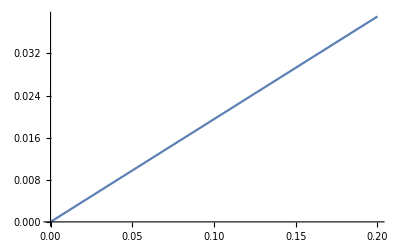

The optimal amount of X to tender is: Δ_X =   202.201

The amount out is: Δ_Y =   -383.255

The resulting reserves are: (x_1,y_1) =   {1202.2,1616.74}

The final price of the pool is: P =   1.80495

The equation to do root finding with is:   ConditionalExpression[-S+(ⅇ^(-(σ^2 τ)/2+√2 σ √τ InverseErfc[(2 (v+x))/(L+v-v γ)]) K (L+x (-1+γ)))/(L+v-v γ)+1/2 K (-1+γ) Erfc[(σ √τ)/(√2)-InverseErfc[(2 (v+x))/(L+v-v γ)]], 0≤(v+x)/(L+v-v γ)≤1]

```mathematica
Subscript[S, ext] = 1.8; Assert[Subscript[S, ext] < Subscript[S, 0]];
Subscript[Prof, Lower][in_] := Subscript[V, A][Subscript[P, M][in,Subscript[Δ, Y][in,Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0],Subscript[γ, 0]]], Subscript[S, ext], in]
Plot[Subscript[Prof, Lower][v], {v,0,0.2}]
Subscript[O, X] = ArgMax[{Subscript[Prof, Lower][x], 0<=x<=Subscript[L, 0]-Subscript[x, 0]}, x]; 
Echo[Subscript[O, X], "The optimal amount of X to tender is: Δ_X = "];
Echo[N[Subscript[Δ, Y][Subscript[O, X],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0],Subscript[γ, 0]],18], "The amount out is: Δ_Y = "];
Echo[{Subscript[x, 0] + Subscript[O, X], Subscript[y, 0] + Subscript[Δ, Y][Subscript[O, X],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0],Subscript[γ, 0]]}, "The resulting reserves are: (x_1,y_1) = "];
Subscript[P, F] = Subscript[P, X][Subscript[x, 0] + Subscript[O, X], Subscript[L, 0] + Subscript[δ, Liq][Subscript[O, X],Subscript[x, 0],Subscript[L, 0],Subscript[γ, 0]], Subscript[K, 0], Subscript[σ, 0], Subscript[τ, 0]]; Echo[N[Subscript[P, F],18], "The final price of the pool is: P = "];
Echo[FullSimplify[D[Subscript[V, A][Subscript[P, M][v,Subscript[Δ, Y][v,x,y,L,K,σ,τ,γ]], S, v],v]], "The equation to do root finding with is: "];
(* Check that the trading function is invariant under the swap *)
Assert[Abs[φ[Subscript[x, 0] + Subscript[O, X], Subscript[y, 0] + Subscript[Δ, Y][Subscript[O, X],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0],Subscript[γ, 0]], Subscript[L, 0] + Subscript[δ, in][Subscript[O, X],Subscript[γ, 0]], Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0]]] < 10^-15]

checkLower[v_,x_,y_,L_,S_,K_,σ_,τ_,γ_]:=-S+(ⅇ^(-(σ^2 τ)/2+√2 σ √τ InverseErfc[(2 x (v+x))/(L (v+x-v γ))]) K x γ)/(v+x-v γ)+(K L (-1+γ) Erfc[(σ √τ)/(√2)-InverseErfc[(2 x (v+x))/(L (v+x-v γ))]])/(2 x);
numOne[v_,x_,y_,L_,S_,K_,σ_,τ_,γ_]:=ⅇ^(-(σ^2 τ)/2+√2 σ √τ InverseErfc[(2 x (v+x))/(L (v+x-v γ))]) K x γ;
denomOne[v_,x_,y_,L_,S_,K_,σ_,τ_,γ_]:=v+x-v γ;
numTwo[v_,x_,y_,L_,S_,K_,σ_,τ_,γ_]:=K L (-1+γ) Erfc[(σ √τ)/(√2)-InverseErfc[(2 x (v+x))/(L (v+x-v γ))]];
denomTwo[v_,x_,y_,L_,S_,K_,σ_,τ_,γ_]:= 2 x;
```

### Raise External Price:

#### Let O_Y be the optimal amount of Y token to tender to get max arbitrage profit.

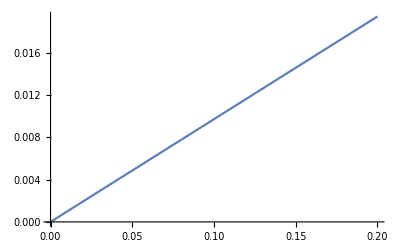

The optimal amount of Y to tender is: Δ_Y =   364.473

The amount out is: Δ_X =   -173.569

The resulting reserves are: (x_1,y_1) =   {826.431,2364.47}

The final price of the pool is: P =   2.19447

The equation to do root finding with is:   ConditionalExpression[-1+(ⅇ^(-(σ^2 τ)/2+√2 σ √τ InverseErfc[(2 (v+y))/(K L+v-v γ)]) S (K L+y (-1+γ)))/(K (K L+v-v γ))+(S (-1+γ) Erfc[(σ √τ)/(√2)-InverseErfc[(2 (v+y))/(K L+v-v γ)]])/(2 K), 0≤(v+y)/(K L+v-v γ)≤1]

```mathematica
Subscript[S, ext] = 2.2; Assert[Subscript[S, ext] > Subscript[S, 0]];
Subscript[Prof, Raise][in_] := Subscript[V, A][Subscript[P, M][Subscript[Δ, X][in,Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0],Subscript[γ, 0]],in], Subscript[S, ext], Subscript[Δ, X][in,Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0],Subscript[γ, 0]]]
Plot[Subscript[Prof, Raise][v], {v,0,0.2}]
Subscript[O, Y] = ArgMax[{Subscript[Prof, Raise][y], 0<=y<=Subscript[K, 0] Subscript[L, 0]-Subscript[y, 0]}, y]; 
Echo[Subscript[O, Y], "The optimal amount of Y to tender is: Δ_Y = "];
Echo[N[Subscript[Δ, X][Subscript[O, Y],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0],Subscript[γ, 0]],18], "The amount out is: Δ_X = "];
Echo[{Subscript[x, 0] + Subscript[Δ, X][Subscript[O, Y],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0],Subscript[γ, 0]], Subscript[y, 0] + Subscript[O, Y]}, "The resulting reserves are: (x_1,y_1) = "];
Subscript[P, F] = Subscript[P, Y][Subscript[y, 0] + Subscript[O, Y], Subscript[L, 0] + 1/Subscript[K, 0] Subscript[δ, in][Subscript[O, Y],Subscript[γ, 0]], Subscript[K, 0], Subscript[σ, 0], Subscript[τ, 0]]; Echo[N[Subscript[P, F], 18], "The final price of the pool is: P = "];
Echo[FullSimplify[D[Subscript[V, A][Subscript[P, M][Subscript[Δ, X][v,x,y,L,K,σ,τ,γ],v], S, Subscript[Δ, X][v,x,y,L,K,σ,τ,γ]],v]], "The equation to do root finding with is: "];
(* Check that the trading function is invariant under the swap *)
Assert[Abs[φ[Subscript[x, 0] + Subscript[Δ, X][Subscript[O, Y],Subscript[x, 0],Subscript[y, 0],Subscript[L, 0],Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0],Subscript[γ, 0]], Subscript[y, 0] + Subscript[O, Y], Subscript[L, 0] + 1/Subscript[K, 0] Subscript[δ, in][Subscript[O, Y],Subscript[γ, 0]], Subscript[K, 0],Subscript[σ, 0],Subscript[τ, 0]]] < 10^-14]
```

## Parameter Updates

### We want to let parameters change, then determine the new L from them.

```mathematica
{Subscript[K, 1],Subscript[σ, 1],Subscript[τ, 1]} = {Subscript[K, 0] + 1/10, Subscript[σ, 0] - 1/20, Subscript[τ, 0]};
Subscript[L, 1] = L /. FindRoot[φ[Subscript[x, 0],Subscript[y, 0],L,Subscript[K, 1],Subscript[σ, 1],Subscript[τ, 1]], {L,Subscript[L, 0]}];
Echo[N[Subscript[L, 0],18], "The original liquidity was: L_0 = "];
Echo[N[Subscript[L, 1],18], "The new liquidity after parameter changes is: L_1 = "];
```

The original liquidity was: L_0 =   1.07205816303780375

The new liquidity after parameter changes is: L_1 =   1.06336